# Data Wrangling, Model Testing, and Model Analysis for Object-Oriented Models in the Wolfram Language

## Workshop # 232 40th International System Dynamics Conference Frankfurt, Germany & Online | July 22, 2022 Guido Wolf Reichert (BSL Management Suport) and Jan Brugård (Wolfram MathCore)

## Introduction

Wolfram Language?! Why should we bring models to programming environments?

### Let’s take 5 minutes to introduce Wolfram Mathematica \[MathematicaIcon] and the Wolfram Language\[WolframLanguageLogo]

#### Functional programming & symbolic computation

Mathematica (the main platform to run the Wolfram Language) is a Computer Algebra System (CAS).
Everything is essentially an expression, where the head can be thought of as a kind of label or type:

head[ e_1, e_2, ...]

Looking at atomic expressions (we cannot split them further into subexpressions), we see that symbols are first class citizens:

```mathematica
Map[AtomQ] @ { 1, 1.2, "Hello", x }
```

{True,True,True,True}

```mathematica
Map[Head] @ { 1, 1.2, "Hello", x }
```

{Integer,Real,String,Symbol}

In the WL we can immediately do symobolic, mathematical computation.

```mathematica
x * x
```

x^2

If we look at the explict or full form, we see that indeed everything is an expression.

```mathematica
a + b c //FullForm
```

Plus[a,Times[b,c]]

Take the antiderivative of a symbolic expression.

```mathematica
Integrate[ 2 Sin[4 x],x ]
```

-1/2 Cos[4 x]

And arrive back at the outset by taking the first derivative.

```mathematica
D[ % , x]
```

2 Sin[4 x]

We could have used natural language input to do this:

WolframAlphaQueryParseResults

-1/2 Cos[4 x]

#### Plotting

We can plot expressions.

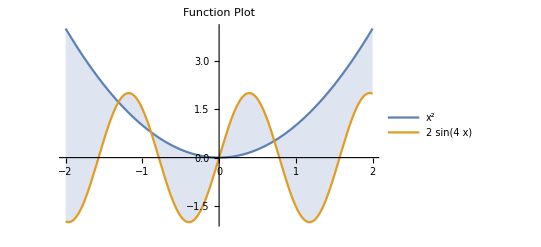

```mathematica
plot = Plot[ { x^2, 2Sin[4 x] }, {x,-2,2}, 
PlotLabel -> Style["Function Plot", "Subtitle", Gray], 
PlotLegends->"Expressions", 
Filling-> {1-> {2}}
]
```

... find the x values for graph intersections.

```mathematica
NSolveValues[ x^2 == 2 Sin[4 x], x, Reals]
```

{-1.31179,-0.886309,0.,0.719873}

And “map” a function over this list to generate a list of tuples (aka points).

```mathematica
points = % //Map[ Function[x, {x, x^2}]]
```

{{-1.31179,1.72078},{-0.886309,0.785544},{0.,0.},{0.719873,0.518218}}

These points can then be added as an “epilog” to the plot.

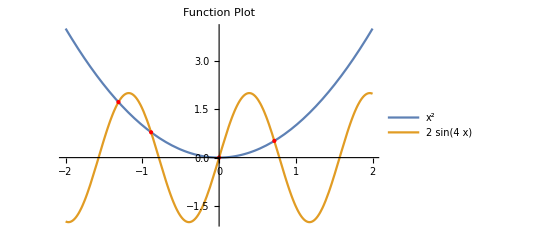

```mathematica
Plot[ { x^2, 2Sin[4 x] }, {x,-2,2}, 
PlotLabel -> Style["Function Plot", "Subtitle", Gray], 
PlotLegends->"Expressions", 
(*Filling-> {1-> {2}},*) 
Epilog->{
Red,
PointSize[Medium],
Point @ points
}
]
```

#### Differential Equations

We can solve elementary symbolic differential equations, for example the following third order expontential delay system:

```mathematica
DSolve[
{
x1'[t] == inflow - x1[t]/(delayTime/3),
x2'[t] == x1[t]/(delayTime/3)-x2[t]/(delayTime/3),
x3'[t] == x2[t]/(delayTime/3)-x3[t]/(delayTime/3),
x1[0]==initialX1,
x2[0]== initialX2,
x3[0]== initialX3
}
,
{ x1, x2, x3}
,
t
]//First /* TableForm
```

x1→Function[{t},1/3 ⅇ^(-(3 t)/delayTime) (-delayTime inflow+delayTime ⅇ^((3 t)/delayTime) inflow+3 initialX1)]
x2→Function[{t},(ⅇ^(-(3 t)/delayTime) (-delayTime^2 inflow+delayTime^2 ⅇ^((3 t)/delayTime) inflow+3 delayTime initialX2-3 delayTime inflow t+9 initialX1 t))/(3 delayTime)]
x3→Function[{t},(ⅇ^(-(3 t)/delayTime) (-2 delayTime^3 inflow+2 delayTime^3 ⅇ^((3 t)/delayTime) inflow+6 delayTime^2 initialX3-6 delayTime^2 inflow t+18 delayTime initialX2 t-9 delayTime inflow t^2+27 initialX1 t^2))/(6 delayTime^2)]

#### Knowledge Representation & Access

A tremendous amount of data can be immediately accessed and processed.

9.63142×10^6 km^2

Often we are interested in a subset of entities, i.e., we apply a filter or a query.

```mathematica
EntityClass["Country","EuropeanUnion"]//EntityList
```

{Austria,Belgium,Bulgaria,Croatia,Cyprus,Czech Republic,Denmark,Estonia,Finland,France,Germany,Greece,Hungary,Ireland,Italy,Latvia,Lithuania,Luxembourg,Malta,Netherlands,Poland,Portugal,Romania,Slovakia,Slovenia,Spain,Sweden}

What are the properties that we may be interested in for the entity “country”?

```mathematica
EntityProperties["Country"]//Short//rasterize
```

-Graphics-

So let’s get the population in 2000 for the countries in the EU and make this a nice looking table using the UN country code to identify countries.

```mathematica
EntityClass["Country","EuropeanUnion"]//RightComposition[
EntityList,
Map @ Function[ country,
<|EntityProperty["Country", "UNCode"]@country ->EntityProperty["Country", "Population", { "Date"-> 2000 }]@country |> 
],
Dataset
]
```

We can also visualize geographic data.

```mathematica
EntityClass["City",{EntityProperty["City","Country"]->Entity["Country","France"],EntityProperty["City","Population"]->GreaterThan[100000]}]//EntityList//Map[Function[entity, Tooltip[ entity, EntityProperty["City", "Name"]@ entity]]]//GeoListPlot
```

-Graphics-

#### Further Information

An Elementary Introduction to the Wolfram Language

Wolfram Language: Fast Introduction for Programmers

Wolfram Language: Fast Introduction for Math Students

Wolfram Language & System Documentation Center

### Building modern data science techniques into modeling software versus importing models into mature data science environments

Houghton and Siegel (2015) in introducing PySD come to the conclusion: 
It makes much more sense to import models to powerful data science environments than to wait until methods are eventually integrated in the system dynamics software.

So how is system dynamics and systems modeling in general integrated into the Wolfram Language?

Systems Modeling is found in the section “Engineering Data & Computation”:

The guide on “System Model Analytics & Design” gets us right into this workshops further topics.

## Model Creation and Import

How can we create system models in the WL and how can we access models that are already built?

### Object–oriented modeling using pre-built components in Wolfram SystemModeler (a quick recap of Workshop #231)

#### Hello World! example using component-based modeling

In Workshop #231 we introduced component-based modeling in Wolfram System Modeler—starting out with a simple Hello World! example.

#### Using classes from the Business Simulation Library (BSL)

The classes for building system dynamics models came from the Business Simulation Library (BSL), which is a modern implementation of system dynamics in Modelica making use of acausal “physical” connectors (think: pipe fittings).

#### Building larger models in a hierarchical fashion

We then showed how larger models can be build in a distributed, object-oriented fashion that is especially amenable to working in a team, to using version control systems like Git, and to documenting models in an integrated fashion (documentation needs to be integrated into the modeling environment, not a separate tool).

### Creating models programmatically in the Wolfram Language

We will not address creating models programmatically in the WL in this workshop, but instead provide a few pointers.

#### Connect pre-built components from within a program

You can use ConnectSystemModelComponents to use pre-built components from a library and connect them to build a SystemModel.

#### Build a model from a systems model

Using CreateSystemModel you can turn a systems model, i.e., a model following a different modeling paradigm, into a SystemModel that can be used and connected as a Modelica model. Systems models can be one of the following:

StateSpaceModel

TransferFunctionModel

AffineStateSpaceModel

NonlinearStateSpaceModel

DiscreteInputOutputModel

Using this you can integrate(partial) models from other domains into your Modelica models—after all, whatever your background, we are interested in dynamical systems.

#### Create a data model by sampling from a function

By sampling from a function to come up with an interpolated curve, CreateDataSystemModel let’s you build an information source for other models to use.

### Importing models

#### Import a textual model written in Modelica

In Workshop #231 we started out with a textual Modelica model for a teacup cooling to room temperature.
Let’s import it as a string (note that strings inside are” escaped” using \ .

```mathematica
$teaCupFromString = ImportString[
"model TeaCupTextual \"Textual model for cooling cup\"
  import BusinessSimulation.Units.{Time,Rate};
  extends BusinessSimulation.Icons.Example;
  // parameters
  parameter Real initTempCup(unit = \"degC\") = 90 \"Initial temperature in the cup\";
  parameter Real tempRoom(unit = \"degC\") = 20 \"Temperature in the room\";
  parameter Time adjTime(displayUnit = \"min\") = 600 \"Time constant for adjustment process\";
  // stock & flow variables
  Real tempCup(start = initTempCup, unit = \"degC\") \"Temperature in the cup is modeled as a stock\";
  Rate heatFlow(displayUnit = \"1/min\") \"Outflow of heat from the cup\";
equation
  heatFlow = (tempRoom - tempCup) / adjTime;
  der(tempCup) = heatFlow;
end TeaCupTextual;"
,
"MO" (* type MO for Modelica models *)
]
```

-Graphics-

Looking at the Modelica code after the input shows that it is interpreted correctly as a model written in the Modelica language.

```mathematica
$teaCupFromString["ModelicaDisplay"]
```

model TeaCupTextual "Textual model for cooling cup"
  import BusinessSimulation.Units.{Time,Rate};
  extends BusinessSimulation.Icons.Example;
  // parameters
  parameter Real initTempCup(unit = "degC") = 90 "Initial temperature in the cup";
  parameter Real tempRoom(unit = "degC") = 20 "Temperature in the room";
  parameter Time adjTime(displayUnit = "min") = 600 "Time constant for adjustment process";
  // stock & flow variables
  Real tempCup(start = initTempCup, unit = "degC") "Temperature in the cup is modeled as a stock";
  Rate heatFlow(displayUnit = "1/min") "Outflow of heat from the cup";
equation
  heatFlow = (tempRoom - tempCup) / adjTime;
  der(tempCup) = heatFlow;
end TeaCupTextual;

#### Importing SystemModeler Archives (.sma) or directly accessing SystemModeler models

In case we do not have SystemModeler installed, we need to import a library or larger model (package.mo) and its data. This is best done using Import or CloudImport and the .sma format that packs models as an archive.

$class = Import[ "filename", "SMA"];
$class = CloudImport[ "uri" ];

If the model has dependencies and is not distributed as a “total model” then we have to make sure that all the dependent libraries are imported as well.

If we have loaded a library or a modeling project in a local installation of SystemModel we can immediately access it.

```mathematica
$teaCupComponentBasedModel = SystemModel["ISDC2022_Workshops.Examples.TeaCupComponentBased1"]
```

-Graphics-

## Model Exploration & Simulation

How can we explore models statically and dynamically?

### A SystemModel has (lots of) properties that we can inspect before we simulate it

Once we have loaded (or created) a SystemModel, we can explore its properties.

```mathematica
Dataset[ SystemModel[ "ISDC2022_Workshops.Examples.TeaCupTextual", "Properties"],DatasetTheme->"Detailed"]//rasterize
```

-Graphics-

#### Summary

A nice summary is given.

```mathematica
SystemModel[ "ISDC2022_Workshops.Examples.TeaCupComponentBased1", "Summary"]//rasterize
```

-Graphics-

#### Icon View

We can access the icon for any class.

```mathematica
SystemModel[ "TeaCupComponentBased1", { "ModelicaIcon", ImageSize -> 200, Frame-> None}]
```

-Graphics-

#### Diagram View

... inspect a model’s diagram.

```mathematica
SystemModel[ "ISDC2022_Workshops.Examples.TeaCupComponentBased2", "Diagram"]
```

-Graphics-

#### Text View

As discussed for entering models above, we can access the Modelica code either as a pure string.

```mathematica
SystemModel["ISDC2022_Workshops.Examples.TeaCupTextual", "ModelicaString" ]
```

model TeaCupTextual "Textual model for cooling cup"
  import BusinessSimulation.Units.{Time,Rate};
  extends BusinessSimulation.Icons.Example;
  // parameters
  parameter Real initTempCup(unit = "degC") = 90 "Initial temperature in the cup";
  parameter Real tempRoom(unit = "degC") = 20 "Temperature in the room";
  parameter Time adjTime(displayUnit = "min") = 600 "Time constant for adjustment process";
  // stock & flow variables
  Real tempCup(start = initTempCup, unit = "degC") "Temperature in the cup is modeled as a stock";
  Rate heatFlow(displayUnit = "1/min") "Outflow of heat from the cup";
equation
  heatFlow = (tempRoom - tempCup) / adjTime;
  der(tempCup) = heatFlow;
  annotation(Documentation(info = "<html>
<p class=\"aside\">This information is part of the ISDC2022 Workshops package.</p>
<p>
This is a stylized model of heat loss for a cup of tea. The model given here is textual only, e.g., there are no components with connections.
</p>
<p>
The temperature in the cup is modeled as a stock (<code>tempCup</code>) with a flow (<code>heatFlow</code>). The outflow of heat, i.e., a negative flow of heat, can be obtained as <code>(tempRoom - tempCup)/adjTime</code>.
</p>
</html>", figures = {Figure(title = "Temperature", identifier = "temp", preferred = true, plots = {Plot(curves = {Curve(y = tempCup)}, __Wolfram_markerAppearances = {MarkerAppearance(marker = "d3d94"), MarkerAppearance(marker = "e4da3")})}, caption = "Tea cup cooling down to room temperature", __Wolfram_markers = {Marker(identifier = "e4da3", position = MarkerPosition(x = 300, xUnit = "s")), Marker(identifier = "d3d94", position = MarkerPosition(x = 600, xUnit = "s"))}, __Wolfram_intervals = {Interval(identifier = "556e0", startMarker = "e4da3", endMarker = "d3d94")})}), experiment(StopTime = 3600, __Wolfram_DisplayTimeUnit = "min"), Diagram(coordinateSystem(extent = {{-148.5, -105}, {148.5, 105}}, preserveAspectRatio = true, initialScale = 0.1, grid = {5, 5}), graphics = {Text(visible = true, origin = {3.28, 10}, rotation = 33.802, textColor = {76, 112, 136}, extent = {{-86.72, -12}, {86.72, 12}}, textString = "textual model only", fontName = "Lato Black")}));
end TeaCupTextual;

... or in a color-coded version. Note, that the annotations—used to store experiment settings, documentation, plots etc.—are nicely hidden behind a » .

```mathematica
SystemModel["ISDC2022_Workshops.Examples.TeaCupTextual", "ModelicaDisplay" ]
```

model TeaCupTextual "Textual model for cooling cup"
  import BusinessSimulation.Units.{Time,Rate};
  extends BusinessSimulation.Icons.Example;
  // parameters
  parameter Real initTempCup(unit = "degC") = 90 "Initial temperature in the cup";
  parameter Real tempRoom(unit = "degC") = 20 "Temperature in the room";
  parameter Time adjTime(displayUnit = "min") = 600 "Time constant for adjustment process";
  // stock & flow variables
  Real tempCup(start = initTempCup, unit = "degC") "Temperature in the cup is modeled as a stock";
  Rate heatFlow(displayUnit = "1/min") "Outflow of heat from the cup";
equation
  heatFlow = (tempRoom - tempCup) / adjTime;
  der(tempCup) = heatFlow;
 »;
end TeaCupTextual;

#### A closer look at model structure and equations

Which components are used in our model?

```mathematica
bslSystemModelComponentDatabase[ $teaCupComponentBasedModel]//Dataset//rasterize
```

-Graphics-

How are they connected to each other?

```mathematica
$teaCupComponentBasedModel["Connections"]
```

{adjTime.y<->heatLoss.u2,heatLoss.y<->losingHeat.u,losingHeat.portB<->cloud.massPort,tempCup.outflow<->losingHeat.portA,tempCup.y2<->tempDifference.u1,tempDifference.y<->heatLoss.u1,tempRoom.y<->tempDifference.u2}

$teaCupComponentBasedModel[Connections]

How does this look in a Graph ?

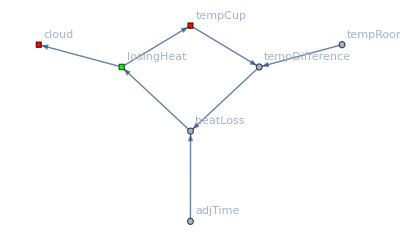

```mathematica
bslSystemModelGraph[ $teaCupComponentBasedModel ]
```

Finally, we can inspect the equations in the model ...

```mathematica
$teaCupComponentBasedModel["SystemEquations",Method-> {"Elimination"-> All}]//DeleteCases[WhenEvent[ ___]]//TableForm
```

-losingHeat.B_rate IndependentPhysicalQuantity[Rate][t]==(tempDifference.y IndependentPhysicalQuantity[][t])/(adjTime.value Time)
tempDifference.y IndependentPhysicalQuantity[][t]==-tempRoom.value IndependentPhysicalQuantity[]+tempCup.x IndependentPhysicalQuantity[][t]
losingHeat.y IndependentPhysicalQuantity[Rate][t]==If[losingHeat.useA_rate IndependentPhysicalQuantity[][t]&&losingHeat.useB_rate IndependentPhysicalQuantity[][t],-losingHeat.B_rate IndependentPhysicalQuantity[Rate][t],0]
tempCup.x IndependentPhysicalQuantity[]'[t]==-losingHeat.y IndependentPhysicalQuantity[Rate][t]

... and find out about the (top level) parameters for a model and their values.

```mathematica
$teaCupTextualModel["TopParameterNames"]
```

{initTempCup IndependentPhysicalQuantity[],tempRoom IndependentPhysicalQuantity[],adjTime Time}

```mathematica
$teaCupTextualModel["ParameterValues"]
```

{initTempCup IndependentPhysicalQuantity[]→90,tempRoom IndependentPhysicalQuantity[]→20,adjTime Time→600}

### Run stored experiments and look at pre-configured plots

#### Using pre-configured plots

In the examples, that we build in the previous workshop, we stored plots and indicated that some of these plots are the default plot. We also set up an experiment for the model, so this information can be used immediately.

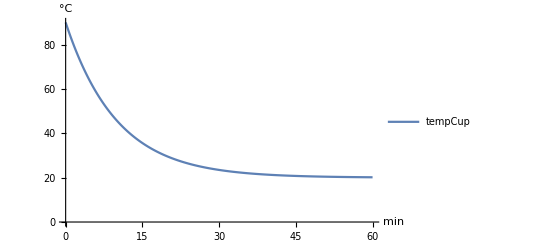
-Graphics-Temperature. Tea cup cooling down to room temperature

```mathematica
SystemModelPlot[ "ISDC2022_Workshops.Examples.TeaCupTextual"]
```

```mathematica
SystemModelPlot[ $]
```

## Working with Models

## Deploying Models

## Helper Functions

#### rasterize

Datasets certainly look nice, but interactivity slows down the front-end; making output a static picture in a sufficient resolution isoften  a good compromise.

```mathematica
rasterize = OperatorApplied[Rasterize][ImageResolution-> 300];
```

#### bslSystemModelComponentDatabase

Come up with an Association (aka “dictionary” in other languages) of a model’s components that can later be used for looking up vars and building bridges back to conventional system dynamics diagramming.

```mathematica
ClearAll[bslSystemModelComponentDatabase];
bslSystemModelComponentDatabase[ model_SystemModel ]:=model["Components"]//RightComposition[
OperatorApplied[Cases][ Element[ name_String, SystemModel[ component_String, True]]:> Association["Name"-> name, "Class" -> component]]
];
```

#### bslSystemModelGraph

Want to look at a causal loop diagram instead?

```mathematica
ClearAll[ bslSystemModelGraph ];
bslSystemModelGraph::usage = "bslSystemModelGraph[model] will return a graph with causal connections shown as directed edges.";
bslSystemModelGraph[ model_SystemModel ] := bslSystemModelGraph[ model["Connections"], bslSystemModelComponentDatabase[ model ] ];
bslSystemModelGraph[ connections_ , componentDatabase_ ]:=
With[
{
inputPattern =  ___~~".u"~~___~~EndOfString,
outputPattern = ___ ~~ ".y" ~~ ___ ~~ EndOfString,
stockQ = Function[ key, componentDatabase//RightComposition[
Query[ SelectFirst[ #Name ==key&], "Class" ],
OperatorApplied[Not@*StringFreeQ]["Stocks"| "Cloud"]
] 
],
flowQ = Function[ key, componentDatabase//RightComposition[
Query[ SelectFirst[ #Name ==key&], "Class" ],
OperatorApplied[Not@*StringFreeQ]["Flows"|"SourcesOrSinks" ]
] 
],
toVertices=Function[ edges, edges//RightComposition[
ReplaceAll[ DirectedEdge[ a_, b_]| UndirectedEdge[a_, b_ ] :>Sequence[a,b]],
Union
]
]
}
,
(* replace input <-> output and output <-> input with directed edges *)
connections//RightComposition[
ReplaceAll[ c1_String <-> c2_String :> c2->c1 /; And[
StringMatchQ[c1, inputPattern ],
StringMatchQ[c2, outputPattern ]
]
],
ReplaceAll[ c1_String <-> c2_String :> c1 -> c2 /; And[
StringMatchQ[c1, outputPattern ],
StringMatchQ[c2, inputPattern ]
]
],
(* get rid of connector names at the end of component names *)
ReplaceAll[x_String :>StringDelete[x,"." ~~___]],
(* make flow <-> stock connections directed edges *)
ReplaceAll[ f_String <-> s_String | s_String <->f_String :> f-> s /; And[
stockQ @ s,
flowQ @ f
]
],
(* draw a graph *)
Function[ edges,
With[
{ 
stockList = Select[ toVertices @ edges,stockQ ],
flowList = Select[ toVertices @ edges, flowQ ]
}
, 
Graph[ edges, 
VertexLabels-> "Name",
VertexShapeFunction-> Union[ Thread[ stockList -> "Square" ], Thread[ flowList -> "Square" ]],
VertexStyle-> Union[ Thread[ stockList -> Red ], Thread[ flowList -> Green ] ]
]
]
]
]
]
```